### In class activity for Chapter 4 Section 2

On paper, compute the gradient of f[x,y]=1/3(x^2 y-x y^2) at the points (x,y)=(2,1), (1,-2), (2,-1) and sketch the gradient with its tail at each respective point on your sketch of the contour graph.

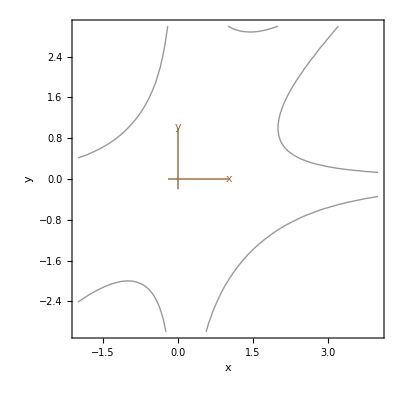

Then work the steps with Mathematica below.

Define the function

```mathematica
Clear[x,y,dx,dy,f,fX,fY,gradf];
Needs["iMultiCalc`iMCUtilities`"]
f[x_,y_]=(x^2 y-x y^2)/3
```

Define the partial derivative functions & gradient vector

```mathematica
fX[x_,y_]=D[f[x,y],x];
fY[x_,y_]=????;
gradf[x_,y_]={fX[x,y],fY[x,y]};
Print["∇f[x,y]=",MatrixForm[gradf[x,y]]]
```

Plot the nonlinear function (see eSection 4.3 for more details.)

```mathematica
topo=ContourPlot[f[x,y],{x,-2,4},{y,-3,3},Contours->{f[2,1],f[1,-2],f[2,-1]},
ContourShading->False,
ContourStyle->Green]
```

Add the arrows

```mathematica
Show[{topo,
Arrow2D[gradf[2,1],Tail->{2,1},Brown],Graphics[{Brown,AbsolutePointSize[5],{Point[{2,1}]}}]
(*add the rest here with commans between commands*)
}]
Print["∇f[",2,",",1,"]=",MatrixForm[gradf[2,1]]]
(*Print the rest here*)
```

### Tangents to Contours

Use Procedure 4.2.1 to work the following exercise step-by-step on paper, then work the computer steps below.

Use this idea to complete Chapter 4 Lab 2.

Contour & Tangent

For each of the functions below:

1)  Sketch the contour f[x,y]=c through the given point (x,y).

2)  Sketch the line tangent to the contour f[x,y]=c at the given point (x,y).

3)  Give the specific local (dx,dy)-equations of that line.

4)  Give the specific (x,y)-equations of that line.

c)  f[x,y]=x y  at the point  (x,y) = (3,2)

Define the function

```mathematica
Clear[x,y,z,dx,dy,dz,f];
Needs["iMultiCalc`iMCUtilities`"];
f[x_,y_]=x y
```

Define the partial derivative functions & gradient vector

```mathematica
fX[x_,y_]=D[f[x,y],x]
```

```mathematica
fY[x_,y_]=??
```

```mathematica
gradf[x_,y_]={fX[x,y],fY[x,y]}
```

Plot the nonlinear function (in local coordinates, see eSection 4.3 for more details.)

Complete the following commands to make a contour plot of f[x+dx,y+dy] near the fixed (x,y)-point, varying the difference values to nearby points by ±2.

```mathematica
x=3;
y=??;
z=f[x,y]
δ=2;
contours=ContourPlot[f[x+dx,y+dy],{dx,-δ,δ},{dy,-δ,δ},FrameLabel->{"dx","dy"}]
```

Where is the (x,y)-point (x,y)=(4,1) on your plot?  (HINT: What is the displacement from (3,2)?)

Next, enter the next set of commands to plot just the single contour thru f[3,2]:

```mathematica
singleCurve=ContourPlot[f[x+dx,y+dy]==f[x,y],{dx,-δ,δ},{dy,-δ,δ},ContourStyle->{AbsoluteThickness[2],Green},FrameLabel->{"dx","dy"}];
singleCurve=Show[{dFrame2D[δ],singleCurve,Graphics[{Red,AbsolutePointSize[5],{Point[{0,0}]}}]}]
```

```mathematica
Show[{contours,singleCurve}]
```

Plot the linear approximation

```mathematica
x=3;
y=2;

δ=2;

dz[dx_,dy_]=gradf[x,y].{dx,dy}

singleLine=ContourPlot[dz[dx,dy]==0,{dx,-δ,δ},{dy,-δ,δ},ContourStyle->{AbsoluteThickness[2],Magenta},FrameLabel->{"dx","dy"}]
```

Your final plot with a scaled gradient vector should look like the following.  Re-enter the command to see if your work above agrees.

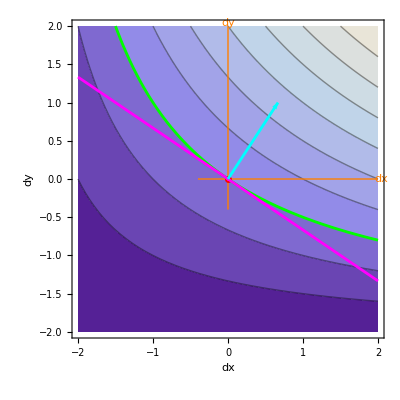

```mathematica
Show[{contours,singleCurve,singleLine,Arrow2D[gradf[x,y]/3,Cyan]}]
```

Plot the tangent and contour near the fixed (x,y) but ±1/10

```mathematica
x=3;
y=2;
z=f[x,y];
δ=1/10;

singleCurve=ContourPlot[f[x+dx,y+dy]==f[x,y],{dx,-δ,δ},{dy,-δ,δ},ContourStyle->{AbsoluteThickness[2],Green},FrameLabel->{"dx","dy"}];

singleLine=ContourPlot[dz[dx,dy]==0,{dx,-δ,δ},{dy,-δ,δ},ContourStyle->{AbsoluteThickness[2],Magenta},FrameLabel->{"dx","dy"}];

Show[{dFrame2D[δ],singleCurve,singleLine,Arrow2D[gradf[x,y]/30,Orange]}]
```

Your graph should look like part of the following.  Why do the contour curve and tangent line look so similar?